# EigenFunctions

## Tyson Jones tyson.jones@monash.edu June 2017

## Paclets Test

```mathematica
Clear["Global`*"]
```

## Import

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
<< PlotFunctions`
<< EigenFunctions`
```

## Plotting Spectra

```mathematica
ShowSpectrum[
	1/2 x^2, {x, -5, 5}, 
	NumberOfModes -> 5, NumberOfPoints -> 200,
	PlotRange -> {0, .6}, PotentialTransform -> (#/20 + .05 &)
]
```

```mathematica
ShowSpectrum[
	0, {-5, 5}, 
	PlotRange -> {0, 0.25}, 
	Potential -> (UnitStep[-#-4.9] + UnitStep[#-4.9]&)
]
```

```mathematica
ShowSpectrum[
	x, {x, -5, 5},
	PotentialTransform -> (#/10 + 5/10 &)
]
```

```mathematica
ShowSpectrum[
	(1 - Exp[- 0.5 (r -4)])^2, {r, 0, 50}, 
	PlotRange -> {0, 0.5}, 
	PotentialTransform  -> (#/3 &),
	NumberOfPoints -> 1000
]
```

```mathematica
ShowSpectrum[
	Exp[-x^2], {x, -5, 5}
]
```

```mathematica
ShowSpectrum[ 
	9999 UnitStep[-(#+2)] + 10 UnitStep[#-2] - 10 UnitStep[#-3] &,
	{-5, 5},
	PotentialTransform -> (#/20 &)
]
```

n = 10 is an interesting state of above, where a maximum appears within a region of greater potential. This may be the threshold where this becomes more energetically favourable than “cramming” more lobes into the region of lesser potential, analogous to oscillator modes of higher energy. That is; gradients (through the Laplacian) are energetic in the Schrodinger equation!

```mathematica
ShowSpectrum[
	10 Exp[-x^2] + x^4/2, 
	{x, -5, 5},
	PotentialTransform -> (#/10 - .2 &)
]
```

```mathematica
ShowSpectrum[
	6 Exp[-x^2] + 4 Exp[-(x-1)^2] - 5 Exp[-(x+1)^2] - 7 Exp[-10^2(x-2)^4] + x^4/2, 
	{x, -5, 5},
	PlotRange -> {0, 1.4},
	PotentialTransform -> (#/20 + .3 &)
]
```

## Interface for GetEigenmodes

## Symbolic Diagonalisations

```mathematica
plotPrev[] :=
	Manipulate[
		PlotWavefunction[ %[[2,n]], { -5, 5}],
		 {n, 1, Length[%[[2]]], 1}
	]
```

```mathematica
GetEigenmodes[
	1/2 x^2, {x, -5, 5},
	NumberOfModes -> 10,
	NumberOfPoints -> 1000,
	TimeSteps -> True
];
plotPrev[]
```

discretising potential  0.00257436

building H matrix  0.053356

diagonalising H matrix  0.00930362

normalising eigenfunctions  0.000604676

```mathematica
GetEigenmodes[
	 x, {x,-5, 5},
	NumberOfModes -> 10,
	NumberOfPoints -> 1000
];
plotPrev[]
```

```mathematica
GetEigenmodes[
	 0, {x,-5, 5},
	NumberOfModes -> 10
];
plotPrev[]
```

```mathematica
GetEigenmodes[
	 0, {-5, 5},
	NumberOfModes -> 10
];
plotPrev[]
```

## Function Diagonalisations

```mathematica
GetEigenmodes[
	1/2#^2&, {-5, 5},
	NumberOfModes -> 30
];
plotPrev[]
```

## Interpolator Diagonalisations

```mathematica
GetEigenmodes[
	ListInterpolation[{1, 2, 3, 4, 5}, {{-5,5}}],
	{-5, 5},
	NumberOfModes ->20
];
plotPrev[]
```

## List Diagonalisations

```mathematica
GetEigenmodes[
	{1, 2, 3, 4, 5},
	{-5, 5},
	NumberOfModes -> 10
];
plotPrev[]
```

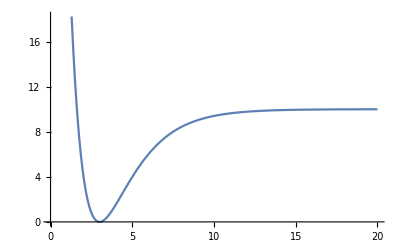

```mathematica
Plot[
	10(1 - Exp[- 0.5 (r -3)])^2,
	{r, 0, 20}
]
```